## @User: ADAPT THIS TO YOUR NEEDS

```mathematica
howManyAtomsInCell=93;
sitestoconsider=Range[1,62];
(*numberofspecies=2; (*Mg Cl*)*)
(*numberofsitesofspecies[#]&/@Range@numberofspecies={62,31};*)
(* remember first timestep has index 1, not 0*)
allsites=Range@howManyAtomsInCell;
sitesCl=Range@62; (* remember that species have not same rlistcutoff *)
sitesMg=Range[63,93];
```

## Extract positions from PIMAIM dumps

```mathematica
positions=
Import["/home/levesque/Recherche/Sels-Fondus/MgCl2/mgcl2-inputs/cageCorrelationFunctions/big/BAK/positions.out"];
nbTimeSteps=(Length@positions)/howManyAtomsInCell; (* nb of dumps in the file *)
coo[whatAtom_Integer, whatTimestep_Integer] :=coo[whatAtom, whatTimestep]=
 positions[[howManyAtomsInCell*(whatTimestep-1) + whatAtom]] (* returns the position of atom 1 at timestep t. Note that 1≤i≤N and 0≤t≤9 *)
allPositionsDumpedAtTimestep[whatTimestep_Integer]:=allPositionsDumpedAtTimestep[whatTimestep]=
coo[#,whatTimestep]&/@Range[howManyAtomsInCell] (* set of all (93) positions vectors at time t *)
```

## Mean Squared Displacement = ensemble average of Squared Euclidean Distance between t0 and t0+t: MSD(t) = ⟨|r_i(t_0)-r_i(t_0+t)|^2⟩_(i,t_0)

```mathematica
msd[site_,t_]:=msd[site,t]=
Mean[SquaredEuclideanDistance[coo[site,#],coo[site,#+t]]&/@Range[nbTimeSteps-t]] (* MSD of each site*)
msdspec[t_]:=msdspec[t]=
Mean[msd[#,t]&/@sitestoconsider] (* msd of each species == mean over all sites of same species*)
```

## Plot the MSD(t)

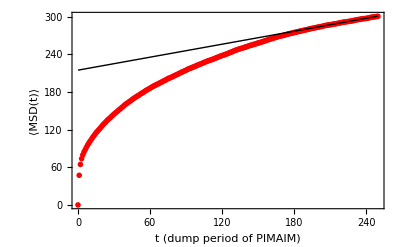

```mathematica
Module[{rangemin=0,rangemax=250},
Show[
ListPlot[
Monitor[
{#,msdspec[#]},
Row[{ProgressIndicator[Dynamic[#],{rangemin,rangemax}],#,rangemax}," /"]
]&/@Range[rangemin,rangemax]
,PlotStyle->{Red,PointSize[0.01]},PlotRange->All,Frame->True,FrameLabel->{"t (dump period of PIMAIM)","⟨MSD(t)⟩"}
],
Plot[Evaluate[Fit[{#,msdspec[#]}&/@Range[200,250],{1,x},x]],{x,rangemin,rangemax},PlotStyle->{Black,Dashed}]
]
]
```

```mathematica
fitmsd=Fit[{#,msdspec[#]}&/@Range[200,250],{1,x},x]
```

214.651+0.34422 x

## Self-diffusion coefficient is

```mathematica
diffusionCoef=(fitmsd[[2]][[1]])/6
```

0.05737